# Seminarska naloga

Opis: S funkcijami izrišemo logo in nato delamo različne transformacije z njim. Možne so tranformacije ki se tičejo funkcij, kar so premiki in raztegi.
Risanje logota: vsaka funkcija predstavla neko krivuljo. Moramo samo najditi pravo krivuljo in če potrebno jo omejiti. Za našo nalogo bomo izrisali logo batman-a.

Risanje logota: 

(predogled)

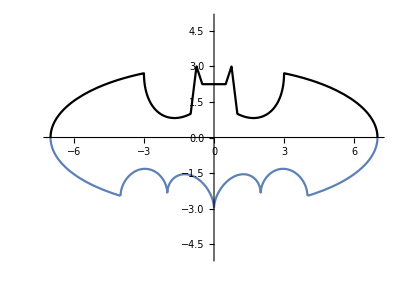

```mathematica
Show[bat1,p2,bat3]
```

1. Za robove kril moramo pravilno omejiti elipso z enačbo (x/7)^2 + (y/3)^2 - 1 = 0, ki zgleda takole:

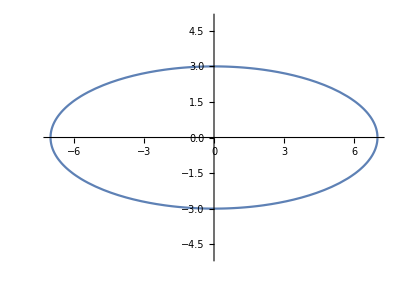

```mathematica
Plot[y /. Solve[(x/7)^2 + (y/3)^2 - 1 == 0], {x,-8,8},PlotRange->{-5,5},AspectRatio->Automatic]
```

Seddaj to elipso če omejimo.

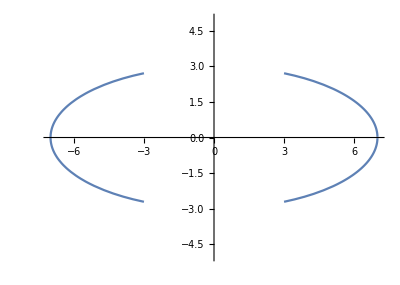

```mathematica
Plot[y /. Solve[(x/7)^2 + (y/3)^2 - 1 == 0], {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>3]]
```

Razdelimo na dele.
Spodnja krila:

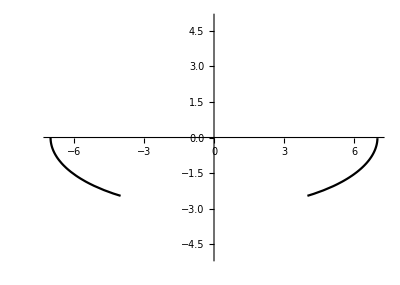

```mathematica
SpodnjaStranskaKrila = -3*√(1-(x/7)^2);
bat1 = Plot[SpodnjaStranskaKrila, {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>4],PlotStyle->Black]
```

Zgornja krila(rabimo za pozneje):

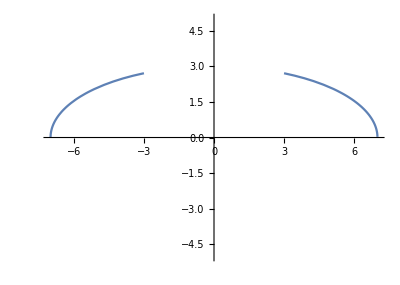

```mathematica
Plot[3*√(1-(x/7)^2), {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>3]]
```

2.

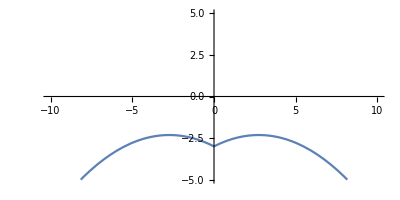

```mathematica
Plot[y /. Solve[y ==Abs[x/2]−(3 √33−7)/112 x^2−3], {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic]
```

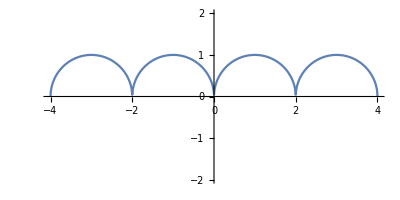

```mathematica
Plot[y /. Solve[y==√(1−(Abs[Abs[x]−2]−1)^2)], {x,-10,10},PlotRange->{-2,2},AspectRatio->Automatic]
```

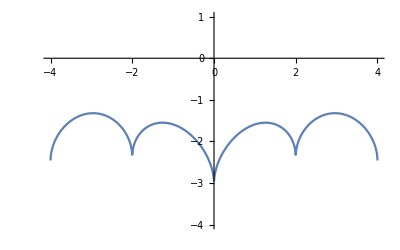

```mathematica
p2 =Plot[y /. Solve[y ==Abs[x/2]−(3 √33−7)/112 x^2−3+√(1−(Abs[Abs[x]−2]−1)^2)], {x,-10,10},PlotRange->{-4,1},AspectRatio->Automatic]
```

The third factor 9 (| (1 − | x |) (| x | −.75) |) (1 − | x |) (| x | −.75) − −−−−−−−−−−−√−8 | x | −y = 0 is just the pair of lines y = 9 - 8 | x | :
√(Abs[(1-Abs[x])(Abs[x]-0.75)]/((1-Abs[x])(Abs[x]-0.75)))

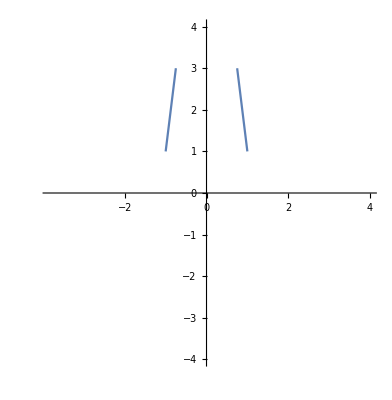

```mathematica
p3 =Plot[y /. Solve[y==9-8Abs[x]], {x,-4,4},PlotRange->{-4,4},AspectRatio-> Full,RegionFunction->Function[{x},0.75<Abs[x]<1]]
```

Similarly, the fourth factor 3 | x | +.75 (| (.75 − | x |) (| x | −.5) | (.75 − | x |) (| x | −.5)) − −−−−−−−−−−−−√−y = 0 is the pair of lines y = 3 | x | +0.75 :
y==0.75 √(Abs[(0.75-Abs[x])(Abs[x]-0.5)]/((0.75-Abs[x])(Abs[x]-0.5)))+3Abs[x]

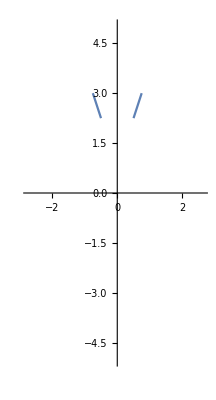

```mathematica
p4 =Plot[y /. Solve[y==3Abs[x]+0.75],{x,-5,5},PlotRange->{-5,5},AspectRatio->Full,RegionFunction->Function[{x},0.5<Abs[x]<0.75]]
```

The fifth factor 2.25 | (.5 − x) (x + .5) | (.5 − x) (x + .5) − −−−−−−−−√−y = 0 is the line y = 2.25 truncated to − 0.5 < x < 0.5.

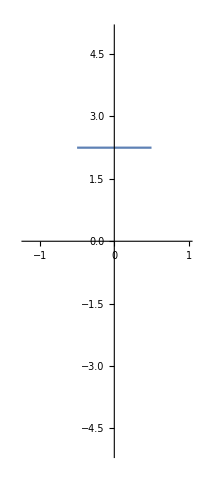

```mathematica
p5 = Plot[y /. Solve[y==2.25],{x,-5,5},PlotRange->{-5,5},AspectRatio->Full,RegionFunction->Function[{x},−0.5<x<0.5]]
```

Finally, 610 √7 + (1.5 − .5 | x |) − (610 √) 144 − (| x | −1) 2 − −−−−−−−−−−√−y = 0 looks like :

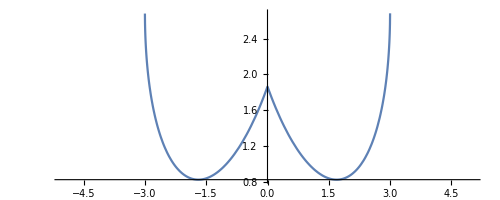

```mathematica
neki2=Plot[y /. Solve[y ==(6 √10)/7+(1.5−0.5Abs[x])-((6 √10)/14)√(4-(Abs[x]-1)^2)], {x,-5,5},AspectRatio->Automatic]
```

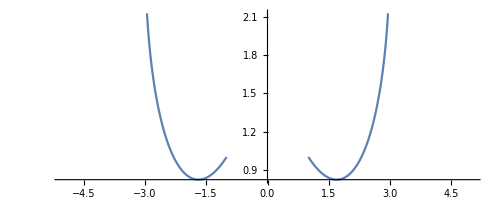

```mathematica
p6 =Plot[y /. Solve[y ==(6 √10)/7+((3−Abs[x])/2)-((3 √10)/7)√(4-(Abs[x]-1)^2)], {x,-5,5},AspectRatio->Automatic,RegionFunction->Function[{x},Abs[x]>1]]
```

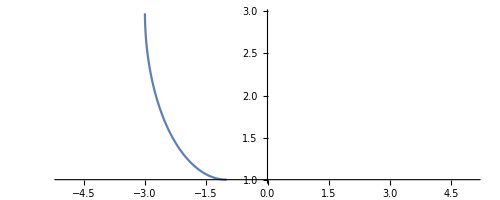

```mathematica
ii =Plot[ -Sqrt[4-(x+1)^2]+3, {x,-5,5},AspectRatio->Automatic,RegionFunction->Function[{x},x<-1]]
```

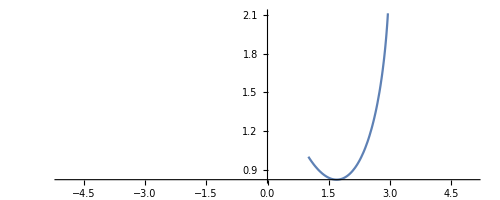

```mathematica
ii2 =Plot[6/7 Sqrt[10]+(3-x)/2-3/7 Sqrt[10] Sqrt[4-(x-1)^2], {x,-5,5},AspectRatio->Automatic,RegionFunction->Function[{x},Abs[x]>1]]
```

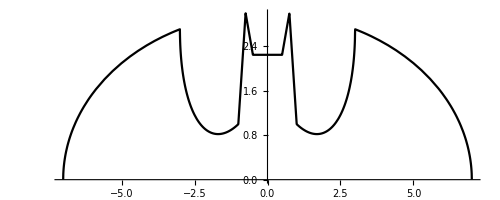

```mathematica
bat3 =Plot[{With[{krila=3*√(1-(x/7)^2),
l=(6 √10)/7+((3+x)/2)-((3 √10)/7)√(4-(Abs[x]-1)^2),
h=(3 (Abs[x-1/2]+Abs[x+1/2]+6)-11 (Abs[x-3/4]+Abs[x+3/4]))/2,

r=(6 √10)/7+((3−x)/2)-((3 √10)/7)√(4-(Abs[x]-1)^2)},krila+(l-krila) UnitStep[x+3]+(h-l) UnitStep[x+1]+(r-h) UnitStep[x-1]+(krila-r) UnitStep[x-3]]},{x,-7,7},AspectRatio->Automatic,PlotStyle->Black]
```

```mathematica
Show[bat1,p2,bat3]
```

-Graphics-